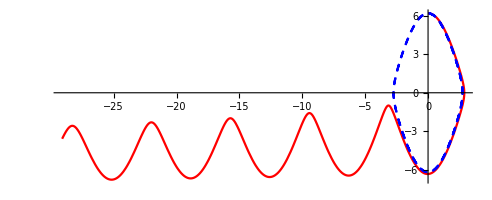

```mathematica
ClearAll["Global'*"]
h=0.01;
tMax = 10;
mtd ="ExplicitEuler";
v0 = 6.2;
(*TODO:
plot energie na čase
Invariants
Simplectic RK
*)
goodSolution =NDSolve[{v'[t]== -10*Sin[y[t]],y'[t]==v[t],v[0]==v0,y[0]==0 },{y[t], v [t]},{t,0,tMax}];
goodPlot = ParametricPlot[Evaluate[{y[t], v [t]} /. goodSolution], {t, 0 ,tMax}, PlotStyle->{Blue,Dashed}];

badSolution =NDSolve[{v'[t]== -10*Sin[y[t]],y'[t]==v[t],v[0]==v0,y[0]==0 },{y[t], v [t]},{t,0,tMax},StartingStepSize->h,Method->{"TimeIntegration"->mtd}];
badPlot =ParametricPlot[Evaluate[{y[t], v [t]} /. badSolution], {t, 0 ,tMax}, PlotStyle->Red];

Show[{badPlot,goodPlot}]
```